# Computational Analysis of the Time Dependent Schroedinger Equation

By: Andrew DeBenedictis, Anna Phillips, and Jen Radoff

## Introduction

## Importing Python-generated data

```mathematica
NotebookDirectory[]
```

/Users/AnnaPhillips/Documents/Tufts Classes/Computational Physics/Project 6/GradStudentsRock_TDSE/

```mathematica
path=NotebookDirectory[];
cases={"freeParticle","squareWell","harmonicOscillator","triangle","kronigPenney","imagPotential","complexPotential","barrier1","barrier2","barrier3","squareWellwithEigenState"};
scheme={"_SFD","_CN"};
numberType={"Real","Imag"};
periodicType={"periodic","nonPeriodic"};
eigenState = {"eValues","eVectors"};
```

## Free Particle

Let’s look at the eigenvalues and eigenvectors to start out siCNe these are scheme-independent:

```mathematica
Clear[freeEVectorsRe,freeEVectorsIm];
Block[{caseChoice,periodicChoice, schemeChoice},
caseChoice=1;
periodicChoice=1;
 schemeChoice=1;
freeEValues=Import[path<>"/Runs/"<>cases⟦caseChoice⟧<>"/"<>periodicType⟦periodicChoice⟧<>scheme⟦schemeChoice⟧<>"_"<>numberType⟦1⟧<>"_"<>eigenState⟦1⟧<>".csv","CSV"];
Do[
Evaluate[Symbol["freeEVectors"<>{"Re","Im"}⟦i⟧]]=Import[path<>"/Runs/"<>cases⟦caseChoice⟧<>"/"<>periodicType⟦periodicChoice⟧<>scheme⟦schemeChoice⟧<>"_"<>numberType⟦i⟧<>"_"<>eigenState⟦2⟧<>".csv","CSV"];,
{i,2}];
freeEVectors=Sqrt[freeEVectorsRe^2+freeEVectorsIm^2];
];
```

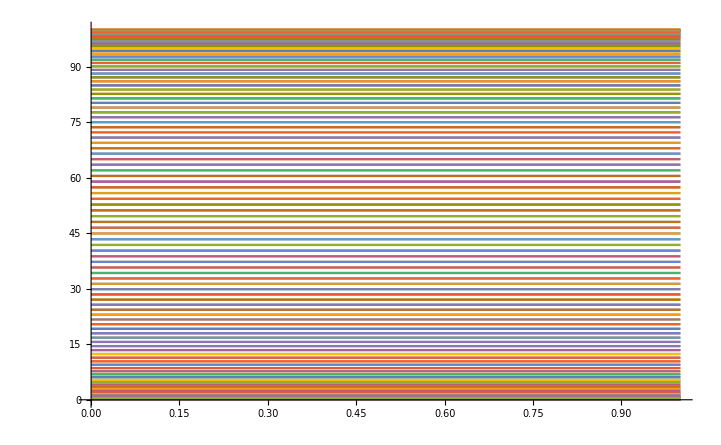

```mathematica
Plot[freeEValues,{x,0,1}]
```

```mathematica
Manipulate[ListPlot[freeEVectors⟦i,All⟧,Joined->True,DataRange->{-20,20}, AxesOrigin->{-20,0}],{i,1,Length[freeEVectors⟦All,1⟧],1}]
```

These look wonky, but that seems possible for the free particle--we should be able to create oscillatory waves at nearly any frequency that would be eigenstates. So it’s probably that the system is underdetermined.

### Scheme 1: Simple Finite DiffereCNe (SFD)

this imports in form {rows, columns} equal to {time, position}

```mathematica
Clear[freeRe,freeIm];
Block[{caseChoice,periodicChoice, schemeChoice},
caseChoice=1;
periodicChoice=1;
 schemeChoice=1;
Do[
Evaluate[Symbol["free"<>{"Re","Im"}⟦i⟧]]=Import[path<>"/Runs/"<>cases⟦caseChoice⟧<>"/"<>periodicType⟦periodicChoice⟧<>scheme⟦schemeChoice⟧<>"_"<>numberType⟦i⟧<>".csv","CSV"] ;,
{i,2}];
free=Sqrt[freeRe^2+freeIm^2];
];
```

```mathematica
Manipulate[ListPlot[{free⟦t,All⟧,freeRe⟦t,All⟧,freeIm⟦t,All⟧},PlotRange->{-.7,.7},PlotLegends->{"|Ψ|^2", "Re(Ψ)","Im(Ψ)"},ImageSize->500,Joined->True,DataRange->{-20,20}, AxesOrigin->{-20,0}],{t,1,Length[freeRe⟦All,1⟧],1}]
```

Well, that seems to not work well. The wave decoheres quickly and flattens within 50 time steps.

### Scheme 2: Crank-Nicolson (CN)

This should be the more stable scheme. For the rest of the cases, we will implement this scheme.

this imports in form {rows, columns} equal to {time, position}

```mathematica
Clear[freeCNRe,freeCNIm];
Block[{caseChoice,periodicChoice, schemeChoice},
caseChoice=1;
periodicChoice=1;
 schemeChoice=2;
Do[
Evaluate[Symbol["freeCN"<>{"Re","Im"}⟦i⟧]]=Import[path<>"/Runs/"<>cases⟦caseChoice⟧<>"/"<>periodicType⟦periodicChoice⟧<>scheme⟦schemeChoice⟧<>"_"<>numberType⟦i⟧<>".csv","CSV"] ;,
{i,2}];
freeCN=Sqrt[freeCNRe^2+freeCNIm^2];
];
```

```mathematica
Manipulate[ListPlot[{freeCN⟦t,All⟧,freeCNRe⟦t,All⟧,freeCNIm⟦t,All⟧},PlotRange->{-.7,.7},PlotLegends->{"|Ψ|^2", "Re(Ψ)","Im(Ψ)"},ImageSize->500,Joined->True,DataRange->{-20,20}, AxesOrigin->{-20,0}],{t,1,Length[freeCNRe⟦All,1⟧],1}]
```

The wave still does decohere, but it takes much longer. We also see it spread out, but doesn’t flatten as before.

#### Let’s compare the two schemes directly

```mathematica
Manipulate[ListPlot[{free⟦t,All⟧,freeCN⟦t,All⟧},PlotRange->{0,.7},Joined->True,PlotLegends->{"Simple finite difference", "Crank-Nicolson"},DataRange->{-20,20}, AxesOrigin->{-20,0}],{t,1,Length[freeCNRe⟦All,1⟧],1}]
```

The flattening effect of the simple finite difference scheme is quite dramatic.

#### and check normalization

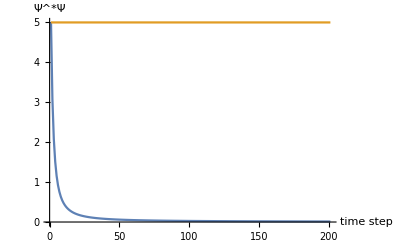

```mathematica
ListPlot[{Total[free^2,{2}],Total[freeCN^2,{2}]},Joined->True,AxesLabel->{"time step","Ψ^*Ψ"}]
```

Scheme 2 doesn’t lose normalization!

### Scheme 2 with non-Periodic boundary conditions

We can see what happens when we effectively put our free particle in a box by fixing the edges.

```mathematica
Clear[freeNonPeriodicCNRe,freeNonPeriodicCNIm];
Block[{caseChoice,periodicChoice, schemeChoice},
caseChoice=1;
periodicChoice=2;
 schemeChoice=2;
Do[
Evaluate[Symbol["freeNonPeriodicCN"<>{"Re","Im"}⟦i⟧]]=Import[path<>"/Runs/"<>cases⟦caseChoice⟧<>"/"<>periodicType⟦periodicChoice⟧<>scheme⟦schemeChoice⟧<>"_"<>numberType⟦i⟧<>".csv","CSV"] ;,
{i,2}];
freeNonPeriodicCN=Sqrt[freeNonPeriodicCNRe^2+freeNonPeriodicCNIm^2];
];
```

```mathematica
Manipulate[ListPlot[{freeNonPeriodicCN⟦t,All⟧,freeNonPeriodicCNRe⟦t,All⟧,freeNonPeriodicCNIm⟦t,All⟧},PlotRange->{-.7,.7},PlotLegends->{"|Ψ|^2", "Re(Ψ)","Im(Ψ)"},ImageSize->500,Joined->True,DataRange->{-20,20}, AxesOrigin->{-20,0}],{t,1,Length[freeNonPeriodicCNRe⟦All,1⟧],1}]
```

PINBALL!!!!

Using the joined option seems to hide the fact that the very end data point does connect to zero.

## Square Well

We’ll look at two versions of the square well: one with our gaussian wave packet, and another with an actual eigenstate (cos(nx/L)).

With a wave packet.

```mathematica
Clear[squareCNRe,squareCNIm,squareCN,squarePotential];
Block[{caseChoice,periodicChoice, schemeChoice},
caseChoice=2;
periodicChoice=2;
 schemeChoice=2;
Do[
Evaluate[Symbol["squareCN"<>{"Re","Im"}⟦i⟧]]=Import[path<>"/Runs/"<>cases⟦caseChoice⟧<>"/"<>periodicType⟦periodicChoice⟧<>scheme⟦schemeChoice⟧<>"_"<>numberType⟦i⟧<>".csv","CSV"] ;,
{i,2}];
squarePotential=Flatten[Import[path<>"/Runs/"<>cases⟦caseChoice⟧<>"/"<>periodicType⟦periodicChoice⟧<>scheme⟦schemeChoice⟧<>"_"<>"Potential"<>".csv","CSV"]];
squareCN=Sqrt[squareCNRe^2+squareCNIm^2];
];
```

```mathematica
Manipulate[ListPlot[{squareCN⟦t,All⟧,squareCNRe⟦t,All⟧,squareCNIm⟦t,All⟧,squarePotential},PlotRange->{-.7,.7},PlotLegends->{"|Ψ|^2", "Re(Ψ)","Im(Ψ)"},DataRange->{-20,20}, AxesOrigin->{-20,0},ImageSize->500,Joined->True],{t,1,Length[squareCNRe⟦All,1⟧],1}]
```

That looks exactly like what we’d expect! Let’s look at our eigenvectors.

```mathematica
Clear[squareEVectorsRe,squareEVectorsIm];
Block[{caseChoice,periodicChoice, schemeChoice},
caseChoice=2;
periodicChoice=2;
 schemeChoice=2;
squareEValues=Import[path<>"/Runs/"<>cases⟦caseChoice⟧<>"/"<>periodicType⟦periodicChoice⟧<>scheme⟦schemeChoice⟧<>"_"<>numberType⟦1⟧<>"_"<>eigenState⟦1⟧<>".csv","CSV"];
Do[
Evaluate[Symbol["squareEVectors"<>{"Re","Im"}⟦i⟧]]=Import[path<>"/Runs/"<>cases⟦caseChoice⟧<>"/"<>periodicType⟦periodicChoice⟧<>scheme⟦schemeChoice⟧<>"_"<>numberType⟦i⟧<>"_"<>eigenState⟦2⟧<>".csv","CSV"];,
{i,2}];
squareEVectors=Sqrt[squareEVectorsRe^2+squareEVectorsIm^2];
];
```

```mathematica
Manipulate[ListPlot[{squareEVectors⟦i,All⟧,squareEVectorsRe⟦i,All⟧,squareEVectorsIm⟦i,All⟧},Joined->True,DataRange->{-20,20}, AxesOrigin->{-20,0},ImageSize->500,PlotRange->Full,PlotLegends->{"|V|", "Re[V]", "Im[V]"}],{i,1,Length[squareEVectors⟦All,1⟧],1}]
```

Okay, so something seems to be wrong with our eigenstate calculating scheme. In our code, the real part of our A matrix is a representation of the Hamiltonian. We’re calculating the eigenvectors of that matrix, but something very, very strange is going on.

#### With an initial cosine wave.

Since we can’t seem to calculate an eigenvector, let’s input it manually.

```mathematica
Clear[squareCosCNRe,squareCosCNIm,squareCosCN,squareCosPotential];
Block[{caseChoice,periodicChoice, schemeChoice},
caseChoice=11;
periodicChoice=2;
 schemeChoice=2;
Do[
Evaluate[Symbol["squareCosCN"<>{"Re","Im"}⟦i⟧]]=Import[path<>"/Runs/"<>cases⟦caseChoice⟧<>"/"<>periodicType⟦periodicChoice⟧<>scheme⟦schemeChoice⟧<>"_"<>numberType⟦i⟧<>".csv","CSV"] ;,
{i,2}];
squareCosPotential=Flatten[Import[path<>"/Runs/"<>cases⟦caseChoice⟧<>"/"<>periodicType⟦periodicChoice⟧<>scheme⟦schemeChoice⟧<>"_"<>"Potential"<>".csv","CSV"]];
squareCosCN=Sqrt[squareCosCNRe^2+squareCosCNIm^2];
];
```

```mathematica
Manipulate[ListPlot[{squareCosCN⟦t,All⟧,squareCosCNRe⟦t,All⟧,squareCosCNIm⟦t,All⟧,squareCosPotential},PlotRange->{-.5,1.2},PlotLegends->{"|Ψ|^2", "Re(Ψ)","Im(Ψ)"},DataRange->{-20,20}, AxesOrigin->{-20,0},ImageSize->500,Joined->True],{t,1,Length[squareCosCNRe⟦All,1⟧],1}]
```

We can see that this is pretty stable, though it does slowly destabalize over time (which is what we’d expect). s

## Harmonic Oscillator

Let’s put our wave packet in a simple harmonic oscilator

```mathematica
Clear[hoCNRe,hoCNIm,hoCN,hoPotential];
Block[{caseChoice,periodicChoice, schemeChoice},
caseChoice=3;
periodicChoice=2;
 schemeChoice=2;
Do[
Evaluate[Symbol["hoCN"<>{"Re","Im"}⟦i⟧]]=Import[path<>"/Runs/"<>cases⟦caseChoice⟧<>"/"<>periodicType⟦periodicChoice⟧<>scheme⟦schemeChoice⟧<>"_"<>numberType⟦i⟧<>".csv","CSV"] ;,
{i,2}];
hoPotential=Flatten[Import[path<>"/Runs/"<>cases⟦caseChoice⟧<>"/"<>periodicType⟦periodicChoice⟧<>scheme⟦schemeChoice⟧<>"_"<>"Potential"<>".csv","CSV"]];
hoCN=Sqrt[hoCNRe^2+hoCNIm^2];
];
```

```mathematica
Manipulate[ListPlot[{hoCN⟦t,All⟧,hoCNRe⟦t,All⟧,hoCNIm⟦t,All⟧,hoPotential/200},PlotRange->{-.7,1},PlotLegends->{"|Ψ|^2", "Re(Ψ)","Im(Ψ)"},ImageSize->500,DataRange->{-20,20}, AxesOrigin->{-20,0},Joined->True],{t,1,Length[hoCNRe⟦All,1⟧],1}]
```

```mathematica
Clear[hoEVectorsRe,hoEVectorsIm];
Block[{caseChoice,periodicChoice, schemeChoice},
caseChoice=3;
periodicChoice=2;
 schemeChoice=2;
hoEValues=Import[path<>"/Runs/"<>cases⟦caseChoice⟧<>"/"<>periodicType⟦periodicChoice⟧<>scheme⟦schemeChoice⟧<>"_"<>numberType⟦1⟧<>"_"<>eigenState⟦1⟧<>".csv","CSV"];
Do[
Evaluate[Symbol["hoEVectors"<>{"Re","Im"}⟦i⟧]]=Import[path<>"/Runs/"<>cases⟦caseChoice⟧<>"/"<>periodicType⟦periodicChoice⟧<>scheme⟦schemeChoice⟧<>"_"<>numberType⟦i⟧<>"_"<>eigenState⟦2⟧<>".csv","CSV"];,
{i,2}];
hoEVectors=Sqrt[hoEVectorsRe^2+hoEVectorsIm^2];
];
```

```mathematica
Manipulate[ListPlot[{hoEVectors⟦i,All⟧,hoEVectorsRe⟦i,All⟧,hoEVectorsIm⟦i,All⟧},Joined->True,DataRange->{-20,20}, AxesOrigin->{-20,0},ImageSize->500,PlotRange->{{-20,20},{-.6,.6}}],{i,1,Length[hoEVectors⟦All,1⟧],1}]
```

Now I can see that our scheme for finding the eigenvectors just isn’t sensible at all. :(

## Triangle

Non-periodic

```mathematica
Clear[triCNRe,triCNIm,triCN,triPotential];
Block[{caseChoice,periodicChoice, schemeChoice},
caseChoice=4;
periodicChoice=2;
 schemeChoice=2;
Do[
Evaluate[Symbol["triCN"<>{"Re","Im"}⟦i⟧]]=Import[path<>"/Runs/"<>cases⟦caseChoice⟧<>"/"<>periodicType⟦periodicChoice⟧<>scheme⟦schemeChoice⟧<>"_"<>numberType⟦i⟧<>".csv","CSV"] ;,
{i,2}];
triPotential=Flatten[Import[path<>"/Runs/"<>cases⟦caseChoice⟧<>"/"<>periodicType⟦periodicChoice⟧<>scheme⟦schemeChoice⟧<>"_"<>"Potential"<>".csv","CSV"]];
triCN=Sqrt[triCNRe^2+triCNIm^2];
];
```

```mathematica
Manipulate[ListPlot[{triCN⟦t,All⟧,triCNRe⟦t,All⟧,triCNIm⟦t,All⟧,triPotential/50},PlotRange->{-.7,.7},PlotLegends->{"|Ψ|^2", "Re(Ψ)","Im(Ψ)"},ImageSize->500,Joined->True,DataRange->{-20,20}, AxesOrigin->{-20,0}],{t,1,Length[triCNRe⟦All,1⟧],1}]
```

## Kronig-Penney

Now let’s do another periodic potential.

```mathematica
Clear[kpCNRe,kpCNIm,kpCN,kpPotential];
Block[{caseChoice,periodicChoice, schemeChoice},
caseChoice=5;
periodicChoice=1;
 schemeChoice=2;
Do[
Evaluate[Symbol["kpCN"<>{"Re","Im"}⟦i⟧]]=Import[path<>"/Runs/"<>cases⟦caseChoice⟧<>"/"<>periodicType⟦periodicChoice⟧<>scheme⟦schemeChoice⟧<>"_"<>numberType⟦i⟧<>".csv","CSV"] ;,
{i,2}];
kpPotential=Flatten[Import[path<>"/Runs/"<>cases⟦caseChoice⟧<>"/"<>periodicType⟦periodicChoice⟧<>scheme⟦schemeChoice⟧<>"_"<>"Potential"<>".csv","CSV"]];
kpCN=Sqrt[kpCNRe^2+kpCNIm^2];
];
Manipulate[ListPlot[{kpCN⟦t,All⟧,kpCNRe⟦t,All⟧,kpCNIm⟦t,All⟧,kpPotential/5},PlotRange->{-.7,1},PlotLegends->{"|Ψ|^2", "Re(Ψ)","Im(Ψ)"},ImageSize->500,Joined->True,DataRange->{-20,20}, AxesOrigin->{-20,0}],{t,1,Length[kpCNRe⟦All,1⟧],1}]
```

The movie looks best if you slow it down--we can see the that the part of the wave packet trapped on one side of one wall goes in one direction, and the part trapped on the other goes in the other direction.

## Barrier

Using the energy output from our python script, we can see that the total enery is about 3.95. Roudning a bit, we’ll say that the energy of the wave is 4 and look at barrier heights of 4, 2, and 6.  Grid size is large compared to barrier width.

### Height = E

```mathematica
Clear[b1CNRe,b1CNIm,b1CN,b1Potential];
Block[{caseChoice,periodicChoice, schemeChoice},
caseChoice=8;
periodicChoice=2;
 schemeChoice=2;
Do[
Evaluate[Symbol["b1CN"<>{"Re","Im"}⟦i⟧]]=Import[path<>"/Runs/"<>cases⟦caseChoice⟧<>"/"<>periodicType⟦periodicChoice⟧<>scheme⟦schemeChoice⟧<>"_"<>numberType⟦i⟧<>".csv","CSV"] ;,
{i,2}];
b1Potential=Flatten[Import[path<>"/Runs/"<>cases⟦caseChoice⟧<>"/"<>periodicType⟦periodicChoice⟧<>scheme⟦schemeChoice⟧<>"_"<>"Potential"<>".csv","CSV"]];
b1CN=Sqrt[b1CNRe^2+b1CNIm^2];
];
Manipulate[ListPlot[{b1CN⟦t,All⟧,b1CNRe⟦t,All⟧,b1CNIm⟦t,All⟧,b1Potential/5},PlotRange->{-.7,1},PlotLegends->{"|Ψ|^2", "Re(Ψ)","Im(Ψ)"},ImageSize->500,Joined->True,DataRange->{-20,20}, AxesOrigin->{-20,0}],{t,1,Length[b1CNRe⟦All,1⟧],1}]
```

If you slow this down, it looks like about half of the wave gets transmitted and the other half gets reflected. Looking at time step 40 (right before the wave starts interacting with the edges), most of the wave has been transmitted. The total normalization is

```mathematica
Total[b1CN[[40,All]]]
```

24.8202696237457491

Our current run has 200 grid points for total grid of 40 unit (meaning each unit is 5 grid points), and the barrier is 1 unit wide. So we want the first 98 grid points for the reflected wave and the last 98 for the transmitted wave.

```mathematica
Dimensions[b1CN[[40]]]
```

{201}

The fraction reflected is

```mathematica
Total[Table[b1CN[[40,i]],{i,1,98}]]/Total[b1CN[[40,All]]]
```

0.531593147230635418

And the fraction transmitted is

```mathematica
Total[Table[b1CN[[40,i]],{i,102,201}]]/Total[b1CN[[40,All]]]
```

0.461862954863236734

So it’s about 50/50, which is what we’d expect. The barrier is a tiny bit higher than

### Height < E

```mathematica
Clear[b2CNRe,b2CNIm,b2CN,b2Potential];
Block[{caseChoice,periodicChoice, schemeChoice},
caseChoice=9;
periodicChoice=2;
 schemeChoice=2;
Do[
Evaluate[Symbol["b2CN"<>{"Re","Im"}⟦i⟧]]=Import[path<>"/Runs/"<>cases⟦caseChoice⟧<>"/"<>periodicType⟦periodicChoice⟧<>scheme⟦schemeChoice⟧<>"_"<>numberType⟦i⟧<>".csv","CSV"] ;,
{i,2}];
b2Potential=Flatten[Import[path<>"/Runs/"<>cases⟦caseChoice⟧<>"/"<>periodicType⟦periodicChoice⟧<>scheme⟦schemeChoice⟧<>"_"<>"Potential"<>".csv","CSV"]];
b2CN=Sqrt[b2CNRe^2+b2CNIm^2];
];
Manipulate[ListPlot[{b2CN⟦t,All⟧,b2CNRe⟦t,All⟧,b2CNIm⟦t,All⟧,b2Potential/5},PlotRange->{-.7,1},PlotLegends->{"|Ψ|^2", "Re(Ψ)","Im(Ψ)"},ImageSize->500,Joined->True,DataRange->{-20,20}, AxesOrigin->{-20,0}],{t,1,Length[b2CNRe⟦All,1⟧],1}]
```

The fraction reflected is

```mathematica
Total[Table[b2CN[[40,i]],{i,1,98}]]/Total[b2CN[[40,All]]]
```

0.319741141235227223

And the fraction transmitted is

```mathematica
Total[Table[b2CN[[40,i]],{i,102,201}]]/Total[b2CN[[40,All]]]
```

0.669631840096473241

Those numbers make sense based on the picture.

### Height > E

```mathematica
Clear[b3CNRe,b3CNIm,b3CN,b3Potential];
Block[{caseChoice,periodicChoice, schemeChoice},
caseChoice=10;
periodicChoice=2;
 schemeChoice=2;
Do[
Evaluate[Symbol["b3CN"<>{"Re","Im"}⟦i⟧]]=Import[path<>"/Runs/"<>cases⟦caseChoice⟧<>"/"<>periodicType⟦periodicChoice⟧<>scheme⟦schemeChoice⟧<>"_"<>numberType⟦i⟧<>".csv","CSV"] ;,
{i,2}];
b3Potential=Flatten[Import[path<>"/Runs/"<>cases⟦caseChoice⟧<>"/"<>periodicType⟦periodicChoice⟧<>scheme⟦schemeChoice⟧<>"_"<>"Potential"<>".csv","CSV"]];
b3CN=Sqrt[b3CNRe^2+b3CNIm^2];
];
Manipulate[ListPlot[{b3CN⟦t,All⟧,b3CNRe⟦t,All⟧,b3CNIm⟦t,All⟧,b3Potential/5},PlotRange->{-.7,1.3},PlotLegends->{"|Ψ|^2", "Re(Ψ)","Im(Ψ)"},ImageSize->500,Joined->True,DataRange->{-20,20}, AxesOrigin->{-20,0}],{t,1,Length[b3CNRe⟦All,1⟧],1}]
```

The fraction reflected is

```mathematica
Total[Table[b3CN[[40,i]],{i,1,98}]]/Total[b3CN[[40,All]]]
```

0.673188816967567468

And the fraction transmitted is

```mathematica
Total[Table[b3CN[[40,i]],{i,102,201}]]/Total[b3CN[[40,All]]]
```

0.322058067125157085

Those numbers make sense based on the picture, and it also makes sense that we’ve got almost exactly the flipped situation from before.

## V=ix

Non-periodic

```mathematica
Clear[imagCNRe,imagCNIm,imagCN,imagPotential];
Block[{caseChoice,periodicChoice, schemeChoice},
caseChoice=6;
periodicChoice=2;
 schemeChoice=2;
Do[
Evaluate[Symbol["imagCN"<>{"Re","Im"}⟦i⟧]]=Import[path<>"/Runs/"<>cases⟦caseChoice⟧<>"/"<>periodicType⟦periodicChoice⟧<>scheme⟦schemeChoice⟧<>"_"<>numberType⟦i⟧<>".csv","CSV"] ;,
{i,2}];
imagPotential=Flatten[Import[path<>"/Runs/"<>cases⟦caseChoice⟧<>"/"<>periodicType⟦periodicChoice⟧<>scheme⟦schemeChoice⟧<>"_"<>"Potential"<>".csv","CSV"]];
imagCN=Sqrt[imagCNRe^2+imagCNIm^2];
];
Manipulate[ListPlot[{imagCN⟦t,All⟧,imagCNRe⟦t,All⟧,imagCNIm⟦t,All⟧,Im[imagPotential]},PlotRange->{-.7,1},PlotLegends->{"|Ψ|^2", "Re(Ψ)","Im(Ψ)"},ImageSize->500,Joined->True,DataRange->{-20,20}, AxesOrigin->{-20,0}],{t,1,Length[complexCNRe⟦All,1⟧],1}]
```

We should be looking at the eigenstates here, but our eigenstate solver is currently broken.

## V=x+ix

Non-periodic

```mathematica
Clear[complexCNRe,complexCNIm,complexCN,complexPotential];
Block[{caseChoice,periodicChoice, schemeChoice},
caseChoice=7;
periodicChoice=2;
 schemeChoice=2;
Do[
Evaluate[Symbol["complexCN"<>{"Re","Im"}⟦i⟧]]=Import[path<>"/Runs/"<>cases⟦caseChoice⟧<>"/"<>periodicType⟦periodicChoice⟧<>scheme⟦schemeChoice⟧<>"_"<>numberType⟦i⟧<>".csv","CSV"] ;,
{i,2}];
complexPotential=Flatten[Import[path<>"/Runs/"<>cases⟦caseChoice⟧<>"/"<>periodicType⟦periodicChoice⟧<>scheme⟦schemeChoice⟧<>"_"<>"Potential"<>".csv","CSV"]];
complexCN=Sqrt[complexCNRe^2+complexCNIm^2];
];
Manipulate[ListPlot[{complexCN⟦t,All⟧,complexCNRe⟦t,All⟧,complexCNIm⟦t,All⟧,complexPotential},PlotRange->{-.7,1},PlotLegends->{"|Ψ|^2", "Re(Ψ)","Im(Ψ)"},ImageSize->500,Joined->True,DataRange->{-20,20}, AxesOrigin->{-20,0}],{t,1,Length[complexCNRe⟦All,1⟧],1}]
```

## Discussion?

About the non-Hermitian-ness...